```mathematica
Needs["PlotLegends`"]
```

((ⅇ^(-(r-μ2)^2/(2 σ2^2)) (Erf[(r+ϵ-μ1)/(√2 σ1)]+Erf[(-r+ϵ+μ1)/(√2 σ1)]))/σ2+(ⅇ^(-(r-μ1)^2/(2 σ1^2)) (Erf[(r+ϵ-μ2)/(√2 σ2)]+Erf[(-r+ϵ+μ2)/(√2 σ2)]))/σ1)/(4 √(2 π))

(ⅇ^(-(-2 r+μ1+μ2)^2/(2 (σ1^2+σ2^2))) (-Erf[((2 r-ϵ-2 μ2) σ1^2-(2 r+ϵ-2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]+Erf[((2 r+ϵ-2 μ2) σ1^2+(-2 r+ϵ+2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]))/(√(2 π) √(σ1^2+σ2^2))

0.582783

0.582783

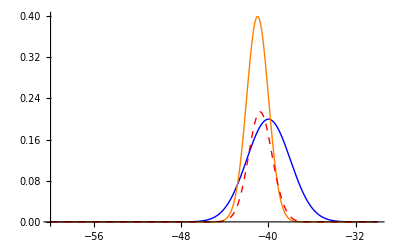

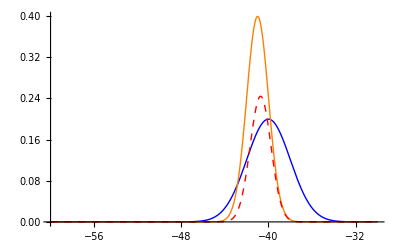

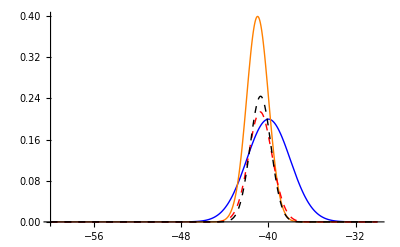

```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ,x,r]
f1[x_]:=(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1);
f2[x_]:=(ⅇ^(-(x-μ2)^2/(2 σ2^2)))/(√(2 π) σ2);
h1[r_]=Integrate[(f1[r-x]*f2[r]+f1[r]*f2[r-x])/2,{x,-ϵ,ϵ}]
gg[r_]=Integrate[f1[r-x/2]*f2[r+x/2],{x,-ϵ,ϵ}]
h3[r_]=Integrate[f1[r-x]*f2[r],{x,-ϵ,ϵ}];
h4[r_]=Integrate[f2[r-x]*f1[r],{x,-ϵ,ϵ}];



μ1=-40;
σ1=2;
μ2=-41;
σ2=1;
ϵ=2;

NIntegrate[h1[x],{x,-50,-30}]
NIntegrate[gg[x],{x,-50,-30}]

Plot[{f1[x],f2[x],h1[x]},{x,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1^M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None]
Plot[{f1[x],f2[x],gg[x]},{x,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1^M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None]
Plot[{f1[x],f2[x],h1[x],gg[x]},{x,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed},{Black,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1^M2(h)1","M1^M2(h)2"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ,x,r]
ff1[x_]:=(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1);
ff2[x_]:=(ⅇ^(-(x-μ2)^2/(2 σ2^2)))/(√(2 π) σ2);
h1[r_]=Integrate[(f1[r-x]*f2[r]+f1[r]*f2[r-x])/2,{x,-ϵ,ϵ}]
gg[r_]=Integrate[f1[r-x/2]*f2[r+x/2],{x,-ϵ,ϵ}]
```

```mathematica
Σ={{Subscript[σ,11]^2,ρ Subscript[σ,11] Subscript[σ,22]},{ρ Subscript[σ,11] Subscript[σ,22],Subscript[σ,22]^2}}
Mean[MultinormalDistribution[{Subscript[μ,1],Subscript[μ,2]},Σ]]
```

{{σ_11^2,ρ σ_11 σ_22},{ρ σ_11 σ_22,σ_22^2}}

{μ_1,μ_2}

```mathematica
MatrixForm[Σ]
```

(σ_11^2 | ρ σ_11 σ_22
ρ σ_11 σ_22 | σ_22^2)

```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ,x,r]
Simplify[(ⅇ^(-(-2 r+μ1+μ2)^2/(2 (σ1^2+σ2^2))) (-Erf[((2 r-ϵ-2 μ2) σ1^2-(2 r+ϵ-2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]+Erf[((2 r+ϵ-2 μ2) σ1^2+(-2 r+ϵ+2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]))/(√(2 π) √(σ1^2+σ2^2))]
```

1/(√(2 π) √(σ1^2+σ2^2))ⅇ^(-(-2 r+μ1+μ2)^2/(2 (σ1^2+σ2^2))) (-Erf[((2 r-ϵ-2 μ2) σ1^2-(2 r+ϵ-2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]+Erf[((2 r+ϵ-2 μ2) σ1^2+(-2 r+ϵ+2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))])

```mathematica
------------------
```

```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ,x,r]
f1[x_]:=(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1);
f2[x_]:=(ⅇ^(-(x-μ2)^2/(2 σ2^2)))/(√(2 π) σ2);
h1[r_]=Integrate[(f1[r-x]*f2[r]+f1[r]*f2[r-x])/2,{x,-ϵ,ϵ}]
gg[r_]=Integrate[f1[r-x/2]*f2[r+x/2],{x,-ϵ,ϵ}]
h3[r_]=Integrate[f1[r-x]*f2[r],{x,-ϵ,ϵ}];
h4[r_]=Integrate[f2[r-x]*f1[r],{x,-ϵ,ϵ}];
```

((ⅇ^(-(r-μ2)^2/(2 σ2^2)) (Erf[(r+ϵ-μ1)/(√2 σ1)]+Erf[(-r+ϵ+μ1)/(√2 σ1)]))/σ2+(ⅇ^(-(r-μ1)^2/(2 σ1^2)) (Erf[(r+ϵ-μ2)/(√2 σ2)]+Erf[(-r+ϵ+μ2)/(√2 σ2)]))/σ1)/(4 √(2 π))

(ⅇ^(-(-2 r+μ1+μ2)^2/(2 (σ1^2+σ2^2))) (-Erf[((2 r-ϵ-2 μ2) σ1^2-(2 r+ϵ-2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]+Erf[((2 r+ϵ-2 μ2) σ1^2+(-2 r+ϵ+2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]))/(√(2 π) √(σ1^2+σ2^2))

```mathematica
Integrate[(ⅇ^(-(-2 r+μ1+μ2)^2/(2 (σ1^2+σ2^2))) (-Erf[((2 r-ϵ-2 μ2) σ1^2-(2 r+ϵ-2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]+Erf[((2 r+ϵ-2 μ2) σ1^2+(-2 r+ϵ+2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]))/(√(2 π) √(σ1^2+σ2^2)),{r,-∞,+∞}]
```

$Aborted

```mathematica
hh[r_]=Integrate[f1[r-x]*f2[r],{r,-∞,∞}]
```

ConditionalExpression[(ⅇ^(-(x+μ1-μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π) σ1 √(1/σ1^2+1/σ2^2) σ2),Re[1/σ1^2+1/σ2^2]>0]

```mathematica
f1
```

f1

```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ,x,r]
f1[x_]:=(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1);
f2[x_]:=(ⅇ^(-(x-μ2)^2/(2 σ2^2)))/(√(2 π) σ2);
Convolve[f1[x],f2[x],x,y]
Integrate[f1[r]*f2[r-x],{r,-∞,∞}]
```

(ⅇ^(-(-y+μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π) σ1 √(1/σ1^2+1/σ2^2) σ2)

ConditionalExpression[(ⅇ^(-(x-μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π) σ1 √(1/σ1^2+1/σ2^2) σ2),Re[1/σ1^2+1/σ2^2]>0]

```mathematica
Simplify[(ⅇ^(-(-y+μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π)  √(σ1^2+σ2^2))]
```

(ⅇ^(-(-y+μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π) √(σ1^2+σ2^2))

```mathematica
f=Integrate[(ⅇ^(-(y-μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π) σ1 √(1/σ1^2+1/σ2^2) σ2),{y,-ϵ,ϵ}]
```

(σ1 √(1/σ1^2+1/σ2^2) σ2 (Erf[(ϵ+μ1-μ2)/(√2 √(σ1^2+σ2^2))]+Erf[(ϵ-μ1+μ2)/(√2 √(σ1^2+σ2^2))]))/(2 √(σ1^2+σ2^2))

```mathematica
μ1=-40.0;
σ1=2.;
μ2=-41;
σ2=1.;
ϵ=2;
f
```

0.582783

```mathematica
1/2 (Erf[41 √(2/5)]-Erf[81/(√10)])
```

1/2 (Erf[41 √(2/5)]-Erf[81/(√10)])

```mathematica
Erf[41 √(2.0/5)]
```

1.